```mathematica
f[x_]:=(x+1)Exp[3/(x+1)];
```

```mathematica
D[f[x],x]
```

ⅇ^(3/(1+x))-(3 ⅇ^(3/(1+x)))/(1+x)

```mathematica
∫_1^3 f[x]ⅆx
```

14 ⅇ^(3/4)-5 ⅇ^(3/2)-9/2 (ExpIntegralEi[3/4]-ExpIntegralEi[3/2])

```mathematica
Series[f[x],{x,1,3}]
```

2 ⅇ^(3/2)-1/2 ⅇ^(3/2) (x-1)+9/16 ⅇ^(3/2) (x-1)^2-27/64 ⅇ^(3/2) (x-1)^3+O[x-1]^4

```mathematica
FindMinimum[f[x],x]
```

{8.15485,{x→2.}}

```mathematica
Limit[f[x]/x,x->∞]
```

1

```mathematica
m=%
```

1

```mathematica
Limit[f[x]-m  x,x->∞]
```

4

```mathematica
k=%
```

4

```mathematica
y[x_]:=m x + k
```

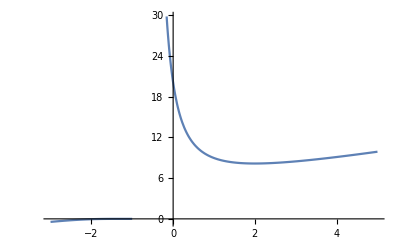

```mathematica
Plot[f[x],{x,-3,5}]
```

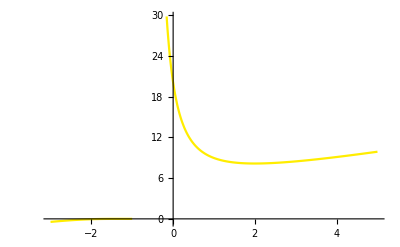

```mathematica
Plot[f[x],{x,-3,5},PlotStyle->RGBColor[1.,0.93,0.]]
```

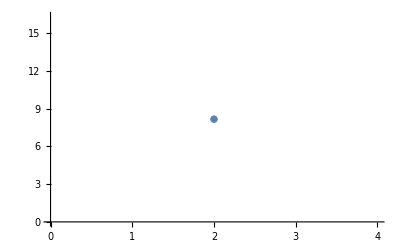

```mathematica
ListPlot[{{2, f[2]}}]
```

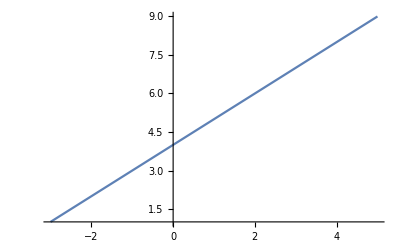

```mathematica
Plot[y[x],{x,-3,5}]
```

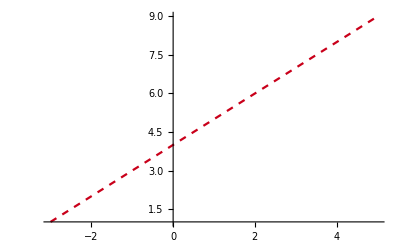

```mathematica
Plot[y[x],{x,-3,5},PlotStyle->Directive[RGBColor[0.79,0.,0.1],Dashed]]
```

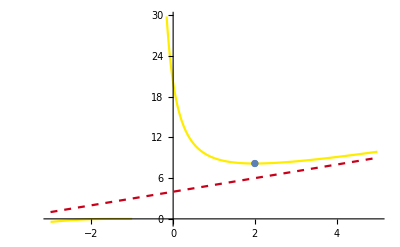

```mathematica
Show[Plot[f[x],{x,-3,5},PlotStyle->RGBColor[1.,0.93,0.]],ListPlot[{{2, f[2]}}],Plot[y[x],{x,-3,5},PlotStyle->Directive[RGBColor[0.79,0.,0.1],Dashed]]]
```

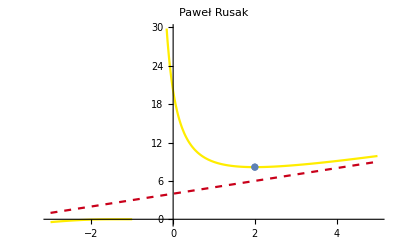

```mathematica
Show[%36,PlotLabel->HoldForm[Paweł Rusak],LabelStyle->{GrayLevel[0]}]
```